```mathematica
SetDirectory[NotebookDirectory[]];
```

# T_scaling

## data

```mathematica
fpi=Flatten[Import["./mub0/buffer/fpi.dat"]];
T0=Flatten[Import["./mub0/buffer/TMeV.dat"]];
t=(T0-T0[[1]])/T0[[1]];
datamub0=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub0=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
b1mub0linear=Transpose[{T0[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
fpi=Flatten[Import["./mub300/buffer/fpi.dat"]];
T300=Flatten[Import["./mub300/buffer/TMeV.dat"]];
t=(T300-T300[[1]])/T300[[1]];
datamub300=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub300=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T300]-2}]]}];
b1mub300linear=Transpose[{T300[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T300]-2}]]}];
fpi=Flatten[Import["./mub400/buffer/fpi.dat"]];
T400=Flatten[Import["./mub400/buffer/TMeV.dat"]];
t=(T400-T400[[1]])/T400[[1]];
datamub400=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub400=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T400]-2}]]}];
b1mub400linear=Transpose[{T400[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T400]-2}]]}];
fpi=Flatten[Import["./mub500/buffer/fpi.dat"]];
T500=Flatten[Import["./mub500/buffer/TMeV.dat"]];
t=(T500-T500[[1]])/T500[[1]];
datamub500=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub500=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T500]-2}]]}];
b1mub500linear=Transpose[{T500[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T500]-2}]]}];
fpi=Flatten[Import["./mub600/buffer/fpi.dat"]];
T600=Flatten[Import["./mub600/buffer/TMeV.dat"]];
t=(T600-T600[[1]])/T600[[1]];
datamub600=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub600=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T600]-2}]]}];
b1mub600linear=Transpose[{T600[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T600]-2}]]}];
```

## Plot

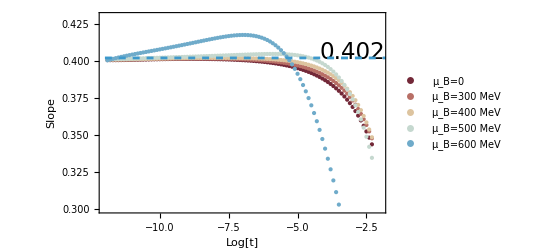

```mathematica
plotT=Show[ListPlot[{b1mub0,b1mub300,b1mub400,b1mub500,b1mub600},
Frame->True,FrameLabel->{Style["Log[t]",25,FontFamily->"Times",Black],Style["Slope",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.2}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_B=0","μ_B=300 MeV","μ_B=400 MeV","μ_B=500 MeV","μ_B=600 MeV"},LabelStyle->16],{0.23,0.32}],
PlotRange->{{-12,-2},{0.3,0.43}},AxesOrigin->{-12,0.3},FrameTicksStyle->Directive[15,Black]],
ListLinePlot[{{-13,0.402},{10,0.402}},PlotStyle->Dashed],ImageSize->700,Background->None,Epilog->{Text[Style["0.402",23],{-3,0.406}]}]
```

```mathematica
dataall={b1mub0,b1mub300,b1mub400,b1mub500,b1mub600};
lineardataall={b1mub0linear,b1mub300linear,b1mub400linear,b1mub500linear,b1mub600linear};
```

```mathematica
Export["./LOdata/mub0.dat",b1mub0];
Export["./LOdata/mub300.dat",b1mub300];
Export["./LOdata/mub400.dat",b1mub400];
Export["./LOdata/mub500.dat",b1mub500];
Export["./LOdata/mub600.dat",b1mub600];
```

```mathematica
Export["./LOdata/t.dat",t]
```

./LOdata/t.dat

```mathematica
Log[0.002/500]
```

-12.4292

```mathematica
0.002/500
```

4.×10^-6